## functions

```mathematica
ToStringWithDateCorrection[expression_]:=If[
Length[StringSplit[ToString[expression],""]]==1,
"0"<>ToString[expression],
ToString[expression]
]
ToStringWithDateCorrection[expression_,correctLength_]:=If[
Length[StringSplit[ToString[expression],""]]<correctLength,
StringRiffle[ConstantArray["0",correctLength-Length[StringSplit[ToString[expression],""]]],""]<>ToString[expression],
ToString[expression]
]
```

```mathematica
MinuteOfDayToHourAndMinuteString[minuteOfDay_]:=ToStringWithDateCorrection[IntegerPart[minuteOfDay/60]]<>":"<>ToStringWithDateCorrection[FractionalPart[minuteOfDay/60]60]
MinuteOfDayToHourAndMinuteList[minuteOfDay_]:={IntegerPart[minuteOfDay/60],FractionalPart[minuteOfDay/60]60}
```

```mathematica
HourAndMinuteToMinuteOfDay[hour_,minute_]:=60hour+minute
```

```mathematica
HourAndMinuteToMinuteOfDay[hourAndMinuteString_]:=If[
StringContainsQ[hourAndMinuteString,":"],
StringSplit[hourAndMinuteString,":"]//ToExpression[#[[1]]]60+ToExpression[#[[2]]]&,
ToExpression[StringTake[hourAndMinuteString,{1,2}]]60+ToExpression[StringTake[hourAndMinuteString,{3,4}]]
]
```

```mathematica
DateExtend[dateObject_,hour_,minute_]:=DateObject[Flatten[{DateList[dateObject][[1;;3]],{hour,minute}}]]
```

```mathematica
(*Function to normalize DateObjects to the same granularity*)
NormalizeDate[date_]:=DateObject[DateList[date][[1;;3]]]

(*Function to find the index of the first element not less than a given date*)
FindFirstIndexNotLessThan[list_,date_]:=Module[{len=Length[list],low=1,high,mid,normDate},normDate=NormalizeDate[date];
high=len;
While[low<high,mid=Quotient[low+high,2];
If[NormalizeDate[First[list[[mid]]]]<normDate,low=mid+1,high=mid];];
low]

(*Function to find the index of the first element greater than a given date*)
FindFirstIndexGreaterThan[list_,date_]:=Module[{len=Length[list],low=1,high,mid,normDate},normDate=NormalizeDate[date];
high=len;
While[low<high,mid=Quotient[low+high,2];
If[NormalizeDate[First[list[[mid]]]]<=normDate,low=mid+1,high=mid];];
low]

(*Define the function to select elements by date range*)
SelectElementsByDateRange[list_,startDate_,endDate_]:=Module[{startIndex,endIndex,normStartDate,normEndDate},(*Normalize dates*)normStartDate=NormalizeDate[startDate];
normEndDate=NormalizeDate[endDate];
(*Find the starting and ending indices*)startIndex=FindFirstIndexNotLessThan[list,normStartDate];
endIndex=FindFirstIndexGreaterThan[list,normEndDate];
(*Return the sublist within the range*)list[[startIndex;;endIndex-1]]]
```

```mathematica
MapFunctionToGranularity[function_,data_List,granularity_String]:=Module[
{extractedComponents,groupedData,mappedData},
(*Extract the relevant component (e.g.,month) from each DateObject and pair with value*)extractedComponents=({DateValue[#[[1]],granularity],#[[2]]}&/@data);
(*Group data by the extracted component and calculate the mean for each group*)
groupedData=GroupBy[extractedComponents,First->Last];
(*Replace each group key with an average value*)
mappedData=function/@groupedData;
SortBy[Transpose[{Keys[mappedData],Values[mappedData]}],First]
]
```

## misc

## heatmeter read-in

```mathematica
ToStringWithDateCorrection[expression_]:=If[
Length[StringSplit[ToString[expression],""]]==1,
"0"<>ToString[expression],
ToString[expression]
]
ToStringWithDateCorrection[expression_,correctLength_]:=If[
Length[StringSplit[ToString[expression],""]]<correctLength,
StringRiffle[ConstantArray["0",correctLength-Length[StringSplit[ToString[expression],""]]],""]<>ToString[expression],
ToString[expression]
]
```

```mathematica
MinuteOfDayToHourAndMinute[minuteOfDay_]:=ToStringWithDateCorrection[IntegerPart[minuteOfDay/60]]<>":"<>ToStringWithDateCorrection[FractionalPart[minuteOfDay/60]60]
```

```mathematica
HourAndMinuteToMinuteOfDay[hour_,minute_]:=60hour+minute
```

```mathematica
HourAndMinuteToMinuteOfDay[hourAndMinuteString_]:=If[
StringContainsQ[hourAndMinuteString,":"],
StringSplit[hourAndMinuteString,":"]//ToExpression[#[[1]]]60+ToExpression[#[[2]]]&,
ToExpression[StringTake[hourAndMinuteString,{1,2}]]60+ToExpression[StringTake[hourAndMinuteString,{3,4}]]
]
```

```mathematica
rawDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\raw";
```

```mathematica
formattedDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\formatted";
```

```mathematica
path=formattedDataRoot;
fileName="heat_stock_net.csv";
lastLoadDay=Module[
{dirs,sortedDirs,foundFile},
(*Get list of directories*)
dirs=FileNames["*",path];
(*Sort directories in decreasing order*)
sortedDirs=Sort[dirs,DateObject[#1]>DateObject[#2]&];
(*Search for the file*)
foundFile=SelectFirst[sortedDirs,FileExistsQ[FileNameJoin[{#,fileName}]]&];
StringSplit[foundFile,"\\"][[-1]]
];
loadDayStamps=Map[StringRiffle[Map[ToStringWithDateCorrection,#[[1;;3]]],"-"]&,DateRange[{2024,2,1},DateObject[lastLoadDay]]];
heatStockDataOriginal=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_stock.csv"]&,
loadDayStamps]]/.{$Failed->"no data"};
heatStockDataNet=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_stock_net.csv"]&,
loadDayStamps]]/.{$Failed->"no data"};
badDays=Flatten[Intersection[Flatten[Position[heatStockDataOriginal,$Failed]],Flatten[Position[heatStockDataNet,$Failed]]]];
goodDays=Complement[Range[Length[loadDayStamps]],badDays];
Manipulate[
Module[
{dayN,timeStamps},
dayN=Position[loadDayStamps,day][[1]][[1]];
timeStamps=Map[
HourAndMinuteToMinuteOfDay[StringTake[#,{-10,-7}]]&,
Select[FileNames[All,rawDataRoot<>"\\"<>day<>"\\heatmeter_images\\"],StringEndsQ[#,".png"]&]
];
Grid[{
{"day","original","net","diff"},
{
loadDayStamps[[dayN]],
If[Dimensions[heatStockDataOriginal[[dayN]]]!={},heatStockDataOriginal[[dayN]][[-1]][[2;;5]],"no data"],
If[Dimensions[heatStockDataNet[[dayN]]]!={},heatStockDataNet[[dayN]][[-1]][[2;;5]],"no data"],
If[Dimensions[heatStockDataOriginal[[dayN]]]!={}&&Dimensions[heatStockDataNet[[dayN]]]!={},heatStockDataNet[[dayN]][[-1]][[2;;5]]-heatStockDataOriginal[[dayN]][[-1]][[2;;5]],"no data"]
},
Table[ListPlot[
{
If[Dimensions[heatStockDataOriginal[[dayN]]]!={},Transpose[Transpose[heatStockDataOriginal[[dayN]]][[{1,1+cycle}]]],Nothing],
If[Dimensions[heatStockDataNet[[dayN]]]!={},Transpose[Transpose[heatStockDataNet[[dayN]]][[{1,1+cycle}]]],Nothing]
},
Joined->True,PlotRange->All,Ticks->{Map[{#,Rotate[MinuteOfDayToHourAndMinute[#],Pi 0.25]}&,Range[0,24 60, 120]],Automatic},ImageSize->250,PlotLabel->"cycle "<>ToString[cycle],Prolog->{If[showCaptures,{Pink,Thin,Map[Line[{{#,0},{#,10000}}]&,timeStamps]}]}
],{cycle,1,4}]
}]
],
{showCaptures,{False,True}},
{{day,loadDayStamps[[goodDays]][[-1]]},loadDayStamps[[goodDays]]}
]
```

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

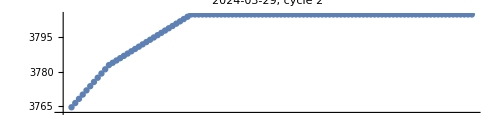
-Graphics-
1500 | 1510 | 1520 | 1530 | 1540 | 1550 | 1600 | 1610 | 1620 | 1630 | 1640 | 1650 | 1700 | 1710 | 1720 | 1730 | 1740 | 1750 | 1800 | 1810 | 1820 | 1830 | 1840 | 1850 | 1900 | 1910 | 1920 | 1930 | 1940 | 1950 | 2000 | 2010 | 2020 | 2030 | 2040 | 2050 | 2100 | 2110 | 2120 | 2130 | 2140 | 2150 | 2200 | 2210 | 2220 | 2230 | 2240 | 2250 | 2300 | 2310 | 2320 | 2330 | 2340 | 2350
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
cycle=2;timeSpan={15,24}100;
day=loadDayStamps[[goodDays]][[-1]];
dayN=Position[loadDayStamps,day][[1]][[1]];
timeStamps=DeleteDuplicates[Map[
ToExpression[StringTake[#,{-10,-7}]]&,
Select[FileNames[All,rawDataRoot<>"\\"<>day<>"\\heatmeter_images\\"],StringEndsQ[#,".png"]&]
]];
cycleImagesForTimeSpan=Map[
Import[rawDataRoot<>"\\"<>day<>"\\heatmeter_images\\"<>ToStringWithDateCorrection[#,4]<>"_"<>ToString[cycle]<>".png"]
&,Select[timeStamps,Between[#,timeSpan]&]];
{
ListPlot[
{
If[Dimensions[heatStockDataOriginal[[dayN]]]!={},Select[Transpose[Transpose[heatStockDataOriginal[[dayN]]][[{1,1+cycle}]]],Between[#[[1]],Map[HourAndMinuteToMinuteOfDay,Map[ToStringWithDateCorrection[#,4]&,timeSpan]]]&],Nothing],
If[Dimensions[heatStockDataNet[[dayN]]]!={},Select[Transpose[Transpose[heatStockDataNet[[dayN]]][[{1,1+cycle}]]],Between[#[[1]],Map[HourAndMinuteToMinuteOfDay,Map[ToStringWithDateCorrection[#,4]&,timeSpan]]]&],Nothing]
},
Ticks->{Map[{#,Rotate[MinuteOfDayToHourAndMinute[#],Pi 0.5]}&,Range[0,24 60, 10]],Automatic},ImageSize->500,AspectRatio->0.25,PlotLabel->day<>", cycle "<>ToString[cycle]
],
{Select[timeStamps,Between[#,timeSpan]&],cycleImagesForTimeSpan}//Grid
}//Column
```

```mathematica
heatFlowDataOriginal=Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_flow.csv"]&,
loadDayStamps];
```

```mathematica
heatFlowDataNet=Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_flow_net.csv"]&,
loadDayStamps];
```

```mathematica
Table[
Table[
ListPlot[
{
Transpose[Transpose[heatFlowDataOriginal[[day]]][[{1,1+cycle}]]],
Transpose[Transpose[heatFlowDataNet[[day]]][[{1,1+cycle}]]]
},
Joined->True,PlotRange->All
]
,{cycle,1,4}]
,{day,goodDays}]//Grid
```

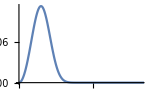
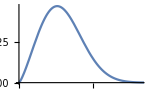
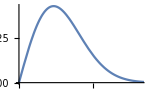
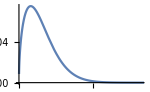

```mathematica
weibullParameters={
{3,10.3,0.001},
{2.3,20,0.001},
{2,20,0.001},
{1.5,10,0.001}
};
Table[Plot[
PDF[WeibullDistribution[weibullParameters[[cycle]][[1]],weibullParameters[[cycle]][[2]],weibullParameters[[cycle]][[3]]],power],{power,0,100},PlotRange->{{0,50},All},ImageSize->150
],{cycle,1,4}]//Row
```

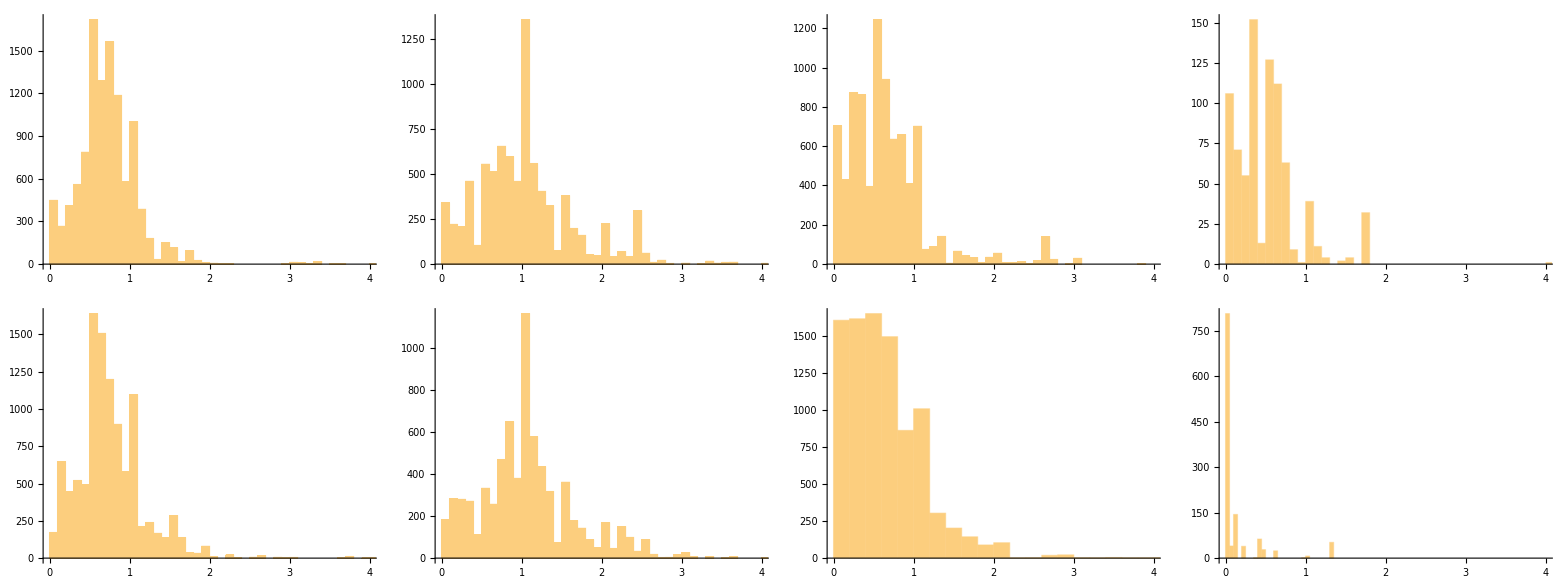

```mathematica
{
Table[
Histogram[
Select[Flatten[Table[
Differences[Transpose[heatStockDataOriginal[[dayN]]][[1+cycle]]]
,{dayN,goodDays}]],0.01<#<100&],PlotRange->{{0,4},All}
],{cycle,1,4}],
Table[
Histogram[
Select[Flatten[Table[
Differences[Transpose[heatStockDataNet[[dayN]]][[1+cycle]]]
,{dayN,goodDays}]],0.01<#<100&],PlotRange->{{0,4},All}
],{cycle,1,4}]
}//Grid
```

## adatok

```mathematica
rawDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\raw";
```

```mathematica
formattedDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\formatted";
```

```mathematica
seasonDays=Map[DateObject,DateRange[{2023,11,8},{2024,5,16}]];
```

## hő

```mathematica
heatDataDays=Map[DateObject,DateRange[{2023,11,22},{2024,3,29}]];
```

```mathematica
heatStockPre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_stock_net.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,heatDataDays]]];
```

```mathematica
heatStockDated=Map[Flatten[#,1]&,Transpose[Table[
Module[
{dayDateList},
dayDateList=DateList[heatDataDays[[dayN]]];
Transpose[Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[heatStockLine[[1]]];
Transpose[{ConstantArray[DateObject[dayDateList],4],heatStockLine[[2;;5]]}]
,{heatStockLine,heatStockPre[[dayN]]}]]
]
,{dayN,1,Length[heatDataDays]}]]];
(*1-es kör átfordulás: jan 20-21*)
(*2-es kör átfordulás: feb 4-5*)
```

```mathematica
cycle=2;
Map[
SortBy[heatStock[[cycle]][[#[[1]];;#[[1]]+1]],First]&,
Map[Position[Differences[Transpose[heatStockDated[[cycle]]][[2]]],#][[1]]&,Select[Differences[Transpose[heatStockDated[[cycle]]][[2]]],#<-10&]]
]
```

{{{Thu 14 Dec 2023 23:55:00GMT+2,4247},{Fri 15 Dec 2023 00:00:00GMT+2,4228.81}},{{Sun 4 Feb 2024 23:55:00GMT+2,9937},{Mon 5 Feb 2024 00:00:00GMT+2,125.}}}

```mathematica
heatStockDated[[1]]=Map[
If[
DateObject[{2024,1,20,23,59}]<#[[1]],
{#[[1]],#[[2]]+10000},
#
]
&,heatStockDated[[1]]];
```

```mathematica
heatStockDated[[2]]=Quiet[Map[
If[
DateObject[{2024,2,4,23,59}]<=#[[1]],
{#[[1]],#[[2]]+10000},
#
]
&,heatStockDated[[2]]]];
```

```mathematica
Export[NotebookDirectory[]<>"\\heatStockDated.mx",heatStock];
```

```mathematica
heatStockSeason=Table[
Transpose[{
Transpose[heatStockDated[[cycle]]][[1]],
Transpose[heatStockDated[[cycle]]][[2]]-heatStockDated[[cycle]][[1]][[2]]
}],{cycle,1,4}];
```

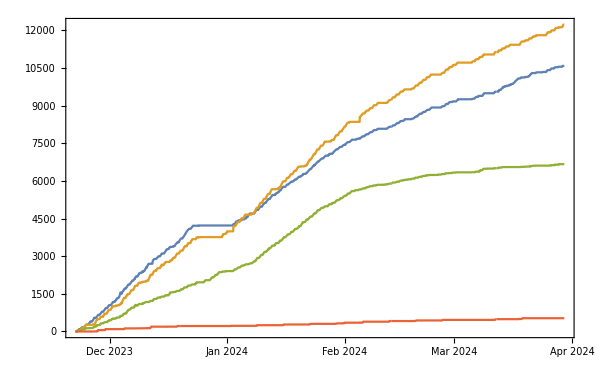

```mathematica
DateListPlot[heatStockSeason]
```

```mathematica
Export[NotebookDirectory[]<>"\\heatStockSeason.mx",heatStockSeason];
```

```mathematica
heatStockSeason=Import[NotebookDirectory[]<>"\\heatStockSeason.mx"];
```

```mathematica
heatStockDaily=Table[Table[
Module[
{dailyCumulative},
dailyCumulative=SelectElementsByDateRange[heatStockSeason[[cycle]],DateExtend[day,0,0],DateExtend[day,23,59]];
If[
dailyCumulative!={},
Transpose[{
Transpose[dailyCumulative][[1]],
Transpose[dailyCumulative][[2]]-dailyCumulative[[1]][[2]]
}],
None]
]
,{day,seasonDays}],{cycle,1,4}];
```

```mathematica
Export[NotebookDirectory[]<>"\\heatStockDaily.mx",heatStockDaily];
```

```mathematica
heatStockDaily=Import[NotebookDirectory[]<>"\\heatStockDaily.mx"];
```

## gáz

```mathematica
gasDataDays=Map[DateObject,Join[
DateRange[{2023,11,23},{2023,12,6}],
DateRange[{2023,12,15},{2024,5,16}]
]];
```

```mathematica
gasStockPre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\gas_stock.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,gasDataDays]]];
```

```mathematica
gasStockDaily=Table[
If[
MemberQ[gasDataDays,day],
Module[
{dayN,dayDateList},
dayN=Position[gasDataDays,day][[1]][[1]];
dayDateList=DateList[gasDataDays[[dayN]]];
Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[gasStockLine[[1]]];
Transpose[{DateObject[dayDateList],gasStockLine[[2]]}]
,{gasStockLine,gasStockPre[[dayN]]}]
],
None
]
,{day,seasonDays}];
```

```mathematica
Export[NotebookDirectory[]<>"\\gasStockDaily.mx",gasStockDaily];
```

```mathematica
gasStockDaily=Import[NotebookDirectory[]<>"\\gasStockDaily.mx"];
```

## szobák hőmérséklete

```mathematica
roomTempDataDays=Map[DateObject,DateRange[{2023,11,8},{2024,5,16}]];
```

```mathematica
roomTempsPre=Table[Quiet[
Map[
Import[formattedDataRoot<>"\\"<>#<>"\\room_"<>ToString[room]<>"_temps.csv"]
&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,roomTempDataDays]]
],{room,1,10}];
```

```mathematica
roomTempsDaily=Table[Table[
If[
MemberQ[roomTempDataDays,day],
Module[
{dayN,dayDateList},
dayN=Position[roomTempDataDays,day][[1]][[1]];
dayDateList=DateList[roomTempDataDays[[dayN]]];
If[
Dimensions[roomTempsPre[[room]][[dayN]]]!={},
Transpose[Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[roomTempLine[[1]]];
Transpose[{ConstantArray[DateObject[dayDateList],4],roomTempLine[[2;;5]]}]
,{roomTempLine,roomTempsPre[[room]][[dayN]]}]],
None
]
],
None
]
,{day,seasonDays}],{room,1,10}];
```

```mathematica
Export[NotebookDirectory[]<>"\\roomTempsDaily.mx",roomTempsDaily];
```

```mathematica
roomTempsDaily=Import[NotebookDirectory[]<>"\\roomTempsDaily.mx"];
```

```mathematica
setTempLowForAtLeastOneRoomDaily=Transpose[
{roomTempDataDays,
Quiet[Map[
Min[#]<0&,
Transpose[Table[
Table[
Min[Select[Transpose[roomTemp[[1]]][[2]]-Transpose[roomTemp[[2]]][[2]],NumberQ]]
,{roomTemp,roomTempsDaily[[room]]}]
,{room,1,10}]]
]]
}];
```

## fűtési állapot

```mathematica
heatingStateDataDays=Map[DateObject,DateRange[{2023,11,8},{2024,5,16}]];
```

```mathematica
heatingStatePre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heating_state.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,heatingStateDataDays]]];
```

```mathematica
heatingStateDaily=Table[
If[
MemberQ[heatingStateDataDays,day],
Module[
{dayN,dayDateList},
dayN=Position[heatingStateDataDays,day][[1]][[1]];
dayDateList=DateList[heatingStateDataDays[[dayN]]];
If[
Dimensions[heatingStatePre[[dayN]]]!={},
Transpose[Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[heatingStateLine[[1]]];
Transpose[{ConstantArray[DateObject[dayDateList],5],heatingStateLine[[2;;6]]}]
,{heatingStateLine,heatingStatePre[[dayN]]}]],
None
]
],
None
]
,{day,seasonDays}];
```

```mathematica
Position[heatingStateDaily,None]
```

{{56},{57},{96},{97},{110},{111},{119},{120},{138},{145},{146},{152},{153},{154},{157},{158},{159},{160},{161},{162},{163},{167},{168},{173},{174},{175},{179},{180},{181},{182},{183},{184},{185},{186},{187},{188},{189},{190},{191},{192}}

```mathematica
heatingStateNoDataDays=heatingStateDataDays[[Flatten[Position[heatingStatePre,$Failed]]]];
```

```mathematica
noHeatingDays=Transpose[Select[setTempLowForAtLeastOneRoomDaily,#[[2]]==False&]][[1]];
```

```mathematica
Table[
Module[
{dayDateList,minutes,blankDayData,dayPosition},
dayDateList=DateList[day];
minutes=Map[
DateObject[Join [dayDateList[[1;;3]],MinuteOfDayToHourAndMinuteList[#]]]&
,Transpose[heatingStatePre[[1]]][[1]]];
blankDayData=ConstantArray[
Transpose[
{
minutes,
ConstantArray[0,288]
}
],5];
dayPosition=Position[seasonDays,day][[1]][[1]];
heatingStateDaily[[dayPosition]]=blankDayData;
]
,{day,Intersection[heatingStateNoDataDays,noHeatingDays]}]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Position[heatingStateDaily,None]
```

{{95},{96},{109},{110},{153},{162},{166},{167},{172},{174}}

```mathematica
Export[NotebookDirectory[]<>"\\heatingStateDaily.mx",heatingStateDaily];
```

```mathematica
heatingStateDaily=Import[NotebookDirectory[]<>"\\heatingStateDaily.mx"];
```

## egyéb

### külső hőmérséklet

```mathematica
externalTempDataDays=Complement[Map[DateObject,DateRange[{2023,11,23},{2024,5,16}]],{DateObject[{2024,1,1,0,0,0.}],DateObject[{2024,3,4,0,0,0.}]}];
```

```mathematica
externalTempPre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\external_temp.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,externalTempDataDays]]];
```

```mathematica
externalTempDaily=Table[
If[
MemberQ[externalTempDataDays,day],
Module[
{dayN,dayDateList},
dayN=Position[externalTempDataDays,day][[1]][[1]];
dayDateList=DateList[externalTempDataDays[[dayN]]];
Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[externalTempLine[[1]]];
Transpose[{DateObject[dayDateList],externalTempLine[[2]]}]
,{externalTempLine,externalTempPre[[dayN]]}]
],
None
]
,{day,seasonDays}];
```

```mathematica
Export[NotebookDirectory[]<>"\\externalTempDaily.mx",externalTempDaily];
```

```mathematica
externalTempDaily=Import[NotebookDirectory[]<>"\\externalTempDaily.mx"];
```

### környezeti változók

```mathematica
energyContentInGasPerCubicMeter=1000 34/3600;(*kWh*)
gasPricePerCubicMeter=700;
```

```mathematica
airSpecificMass=1.2;(*kg/m3*)
```

```mathematica
airSpecificHeatCapacity=1012;(*J/kg/K*)
```

```mathematica
roomNames={"ovi","PK","SZGK","Gólyairoda","Mérce","vendégtér","kisterem","trafóház","Oktopusz","Lahmacun","Kazán közös terek","műhely"};
```

```mathematica
roomsWithTempData={1,2,3,4,5,6,7,9,10};
```

```mathematica
roomToCycle={1,1,2,2,2,3,3,4,1,2};
```

```mathematica
roomAreas={53,26,29,26.5,72,100,60.25,240,66,24,50,26.5} ;
```

```mathematica
roomExternalWallLength={9.8,4.8,5.4,6,10.2,15.4,10.2,25,12.5,5.2,None,2.5} ;
```

```mathematica
roomHeight=3.2;
```

```mathematica
radiatorHeight=0.6;
roomRadiatorLength={4 140,280,300,180,540+150,6 120,4 120,0,2 140,100}/100;
```

## elemzés

## jegyzetek

úgy érdemes tekinteni, mint egy cél felé hajtott rendszert

kontrollváltozók:
	- fő kontrollváltozók: fogyasztott gáz és kiküldött hő
		> korrellált kontrollváltozók: fűtési állapot
	- nem irányított kontrollváltozó: kinti hőmérséklet, besugárzás
függő változók: szobák hőmérséklete

hibajel: beállított hőmérséklet - aktuális hőmérséklet

fő kérdések:
- milyen költséggel milyen mértékben lehet csökkenteni a hibát?
- hogy teljesít a rendszer, lehet-e jellemezni valahogy?
- külső körülmények hogyan befolyásolják?
- van-e olyan szcenárió, amivel jelentősen jobban teljesítene?
- lehet-e jellemezni a szobákat?
- hogyan viszonyul a tavalyi adatokhoz?

- pontosítani a szobák hőtechnikai jellemzőit (homennyisegbol becsülni? figyelembe venni aktuális hőmérsékletet hokapacitashoz? fűtővíz hőmérséklete?)
- karakterizalni, h milyen költsége van  egy szoba felfutesenek adott külső hőmérséklet mellett 
- jellemezni a szitut költség - komfort síkon, akár szezonon belül is
- modellezni, hogy szabályozás vagy beavatkozás mennyit tol a síkon milyen irányba

## gázból hő

### nem fűtésre elmenő gáz becslése

```mathematica
gasFlowAndHeatingStateDaily=Select[Quiet[Table[
Module[
{gasDataPosition,heatingStateDataPosition},
gasDataPosition=Position[gasDataDays,day];
heatingStateDataPosition=Position[heatingStateDataDays,day];
If[
Dimensions[gasStockDaily[[gasDataPosition[[1]][[1]]]]]!={},
Transpose[Join[
{
Drop[Transpose[gasStockDaily[[gasDataPosition[[1]][[1]]]]][[1]],1],
Differences[Transpose[gasStockDaily[[gasDataPosition[[1]][[1]]]]][[2]]]
},
Map[
Drop[Transpose[#][[2]],1]
&,heatingStateDaily[[heatingStateDataPosition[[1]][[1]]]]]
]],
None
]
],{day,seasonDays}]],Length[Dimensions[#]]>1&];
```

```mathematica
gasConsumptionByHeatingState=Table[
Transpose[Transpose[Select[
Flatten[gasFlowAndHeatingStateDaily,1],
#[[3]]==heatingState&
]][[{1,2}]]],{heatingState,0,1}];
```

```mathematica
nonHeatingProportionOfGasConsumption=Mean[Transpose[gasConsumptionByHeatingState[[1]]][[2]]]/Total[Mean[Transpose[gasConsumptionByHeatingState[[1]]][[2]]]+Mean[Transpose[gasConsumptionByHeatingState[[2]]][[2]]]];
```

```mathematica
nonHeatingProportionOfGasConsumption=0.3707982073738875;
heatingProportionOfGasConsumption=1-nonHeatingProportionOfGasConsumption;
```

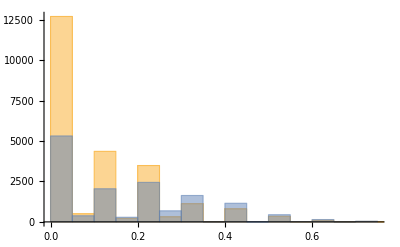

```mathematica
Histogram[
{
Transpose[gasConsumptionByHeatingState[[1]]][[2]],
Transpose[gasConsumptionByHeatingState[[2]]][[2]]
}]
```

```mathematica
typicalDailyGasConsumptionByMonthByHeatingState=Table[Table[
Transpose[Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,
Select[
gasConsumptionByHeatingState[[heating]],
DateValue[#[[1]],"Month"]==month&
],"Hour"]]]
,{heating,1,2}],{month,{11,12,1,2,3,4}}];
```

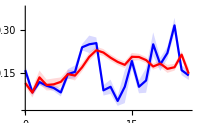
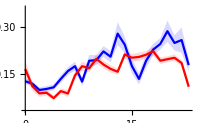
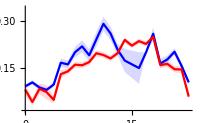
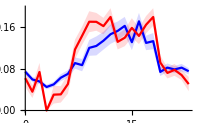
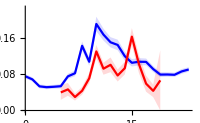
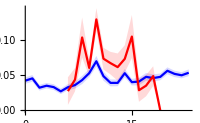

```mathematica
Table[
ErrorListPlot[
typicalDailyGasConsumptionByMonthByHeatingState[[month]],
{Blue,Red},
{ImageSize->200,PlotLegends->{"nincs fűtés","van fűtés"}},
{True,True,False}
],{month,1,6}]
```

```mathematica
typicalDailyGasConsumptionByHeatingState=Table[
Transpose[Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,
gasConsumptionByHeatingState[[heating]],"Hour"]]]
,{heating,1,2}];
```

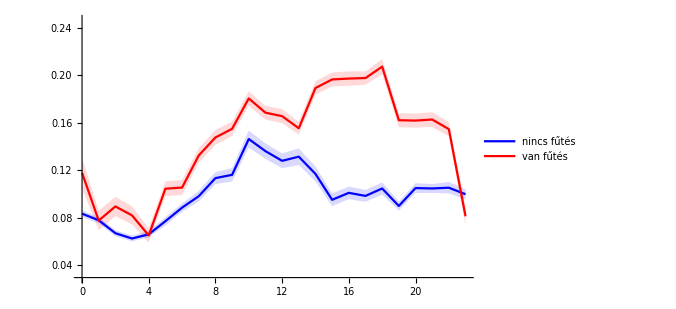

```mathematica
ErrorListPlot[
typicalDailyGasConsumptionByHeatingState,
{Blue,Red},
{ImageSize->500,PlotLegends->{"nincs fűtés","van fűtés"}},
{True,True,False}
]
```

```mathematica
typicalWeeklyGasConsumptionByHeatingState=Table[
Transpose[
Map[
{#[[1]],#[[2]],#[[3]]}&,
SortBy[
Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,gasConsumptionByHeatingState[[heating]],"DayName"]/.{Monday->1,Tuesday->2,Wednesday->3,Thursday->4,Friday->5,Saturday->6,Sunday->7}]
,First]
]
]
,{heating,1,2}];
```

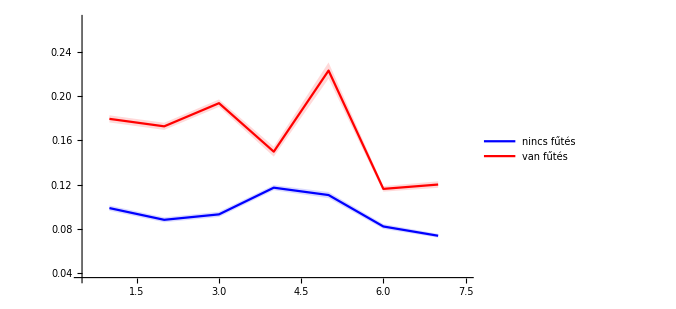

```mathematica
ErrorListPlot[
typicalWeeklyGasConsumptionByHeatingState,
{Blue,Red},
{ImageSize->500,PlotLegends->{"nincs fűtés","van fűtés"}},
{True,True,False}
]
```

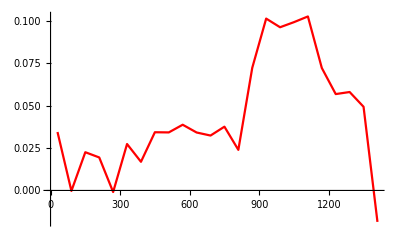

```mathematica
ListPlot[Transpose[{
typicalDailyGasConsumptionByHeatingState[[1]][[1]]60+30,
typicalDailyGasConsumptionByHeatingState[[2]][[2]]-typicalDailyGasConsumptionByHeatingState[[1]][[2]]
}],Joined->True,PlotStyle->Red]
```

```mathematica
NonHeatingGasConsumption[minute_]:=Quiet[Interpolation[
Transpose[{
typicalDailyGasConsumptionByHeatingState[[1]][[1]]60+30,
typicalDailyGasConsumptionByHeatingState[[1]][[2]]
}],InterpolationOrder->0
][minute]]
```

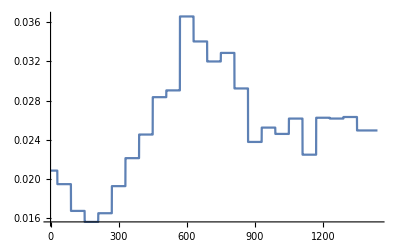

```mathematica
Plot[
NonHeatingGasConsumption[minute]/4,{minute,0,24 60}
]
```

```mathematica
Total[Table[
NonHeatingGasConsumption[minute],
{minute,0,60 24-5,5}]]/4
```

7.25604

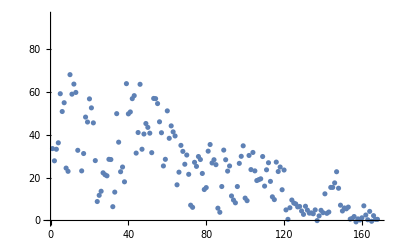

```mathematica
ListPlot[
Map[
Transpose[#][[2]][[-1]]-Total[Table[
NonHeatingGasConsumption[minute]/4,
{minute,0,60 24-5,5}]]
&,DeleteCases[gasStockDaily,None]]
]
```

```mathematica
totalGasTotalHeatDaily=Table[
{
day[[1]][[-1]][[2]] energyContentInGasPerCubicMeter,
Total[Table[day[[2]][[cycle]][[-1]][[2]],{cycle,1,4}]]
}
,{day,gasAndHeatStockDaily}];
```

```mathematica
Fit[totalGasTotalHeatDaily,{1,x},x]
```

0.193335+0.601838 x

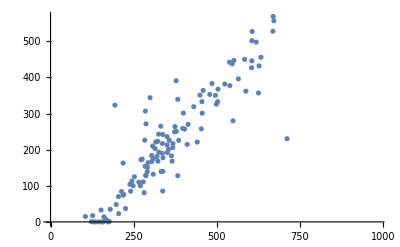

```mathematica
ListPlot[totalGasTotalHeatDaily]
```

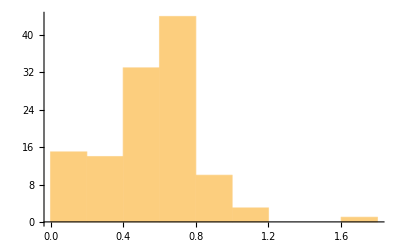

```mathematica
Histogram[Map[#[[2]]/#[[1]]&,totalGasTotalHeatDaily]]
```

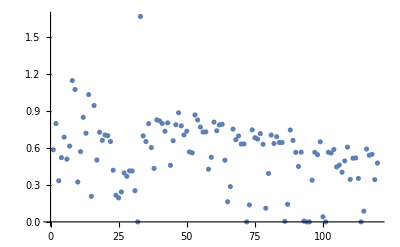

```mathematica
ListPlot[Map[#[[2]]/#[[1]]&,totalGasTotalHeatDaily]]
```

### kazánok hatékonyságának becslése

```mathematica
gasStockAndHeatStockDaily=Quiet[Table[
If[
Dimensions[gasStockDaily[[dayN[[1]][[1]]]]]!={}&&Dimensions[heatStockDaily[[1]][[dayN[[1]][[1]]]]]!={},
{
gasStockDaily[[dayN[[1]][[1]]]],
Table[heatStockDaily[[cycle]][[dayN[[1]][[1]]]],{cycle,1,4}]
},
None
],{dayN,1,Length[seasonDays]}]];
```

```mathematica
heatingProportionOfGasConsumption
```

0.629202

```mathematica
boilerEfficiencyHourlyByDay=Quiet[ Select[Table[
Transpose[{
Map[DateObject[Join[DateList[Transpose[dayData[[1]]][[1]][[1]]][[1;;3]],{#,30,0}]]&,Range[0,23]],
Transpose[MapFunctionToGranularity[Total,Transpose[{Drop[Transpose[dayData[[1]]][[1]],1],Total[Table[Differences[Transpose[dayData[[2]][[cycle]]][[2]]],{cycle,1,4}]]}],"Hour"]][[2]]/(0.75 Transpose[MapFunctionToGranularity[Total,Transpose[{Drop[Transpose[dayData[[1]]][[1]],1],Differences[Transpose[dayData[[1]]][[2]]]}],"Hour"]][[2]] energyContentInGasPerCubicMeter)
}],{dayData,DeleteCases[gasStockAndHeatStockDaily,None]}],NumberQ[Total[Transpose[#][[2]]]]&]];
```

```mathematica
meanBoilerEfficiencyByDay=Table[
Select[Transpose[dayData][[2]],NumberQ[#]&&0<#&]//If[#!={},{NormalizeDate[dayData[[1]][[1]]],Mean[#]},Nothing]&
,{dayData,boilerEfficiencyHourlyByDay}];
```

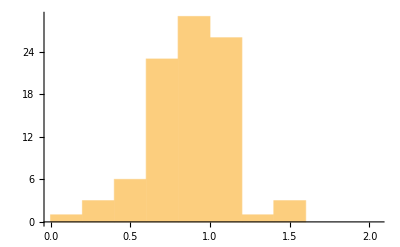

```mathematica
Histogram[Transpose[meanBoilerEfficiencyByDay][[2]]]
```

```mathematica
boilerEfficiencyEstimate=Mean[Transpose[meanBoilerEfficiencyByDay][[2]]];
boilerEfficiencyEstimate=0.9835433845947968;
```

Part::partw: Part 2 of Transpose[meanBoilerEfficiencyByDay] does not exist.

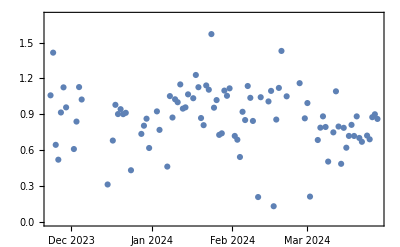

```mathematica
DateListPlot[meanBoilerEfficiencyByDay,Joined->False]
```

## szobák hődinamikája

```mathematica
HeatingCurve[externalTemp_,maxTemp_,minTemp_]:=Module[{supplyTemp},(*Define the relationship between external temperature and supply water temperature*)supplyTemp=If[externalTemp<=-10,maxTemp,If[externalTemp>=25,minTemp,maxTemp-(maxTemp-minTemp)/(25+10)(externalTemp+10)]];
supplyTemp]
```

### hőtehetetlenségi tényezők becslése

```mathematica
calculationDays=Intersection[heatingStateDataDays,roomTempDataDays,externalTempDataDays];
```

#### hűlés

```mathematica
roomCoolingData=Table[Select[Flatten[Quiet[Table[
Module[
{dayN},
dayN=Position[seasonDays,day][[1]][[1]];
If[
Dimensions[roomTempsDaily[[room]][[dayN]]]!={}&&Dimensions[externalTempDaily[[dayN]]]!={}&&Dimensions[heatingStateDaily[[dayN]]]!={},
Transpose[Transpose[Select[Transpose[{
Transpose[heatingStateDaily[[dayN]][[1+roomToCycle[[room]]]]][[2]],
Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]]-Transpose[externalTempDaily[[dayN]]][[2]],
Join[{n},Differences[Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]]]/5]
}],#[[1]]==0&&#[[3]]<=0&&NumberQ[#[[2]]]&&NumberQ[#[[3]]]&]][[{2,3}]]],
None
]
]
,{day,calculationDays}]],1],Length[#]==2&],{room,1,10}];
```

```mathematica
Map[Length,roomCoolingData]
```

{20489,22185,25019,25387,14193,17439,24171,0,2320,5831}

```mathematica
roomCoolingCoefficients=Table[
Module[
{roomHeatCapacity,roomExternalWallArea,heatLossInJPerMin,heatLossInWatts,heatTransferCoefficient},
roomHeatCapacity=roomAreas[[room]]roomHeight airSpecificMass airSpecificHeatCapacity;
roomExternalWallArea=roomExternalWallLength[[room]]roomHeight;
heatLossInJPerMin=roomHeatCapacity (-Transpose[roomCoolingData[[room]]][[2]]);
heatLossInWatts=heatLossInJPerMin/60;
heatTransferCoefficient=heatLossInWatts/(roomExternalWallArea Transpose[roomCoolingData[[room]]][[1]]);
Select[heatTransferCoefficient,NumberQ]
],{room,1,10}];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

```mathematica
roomCoolingCoefficientEstimates=Map[Mean,roomCoolingCoefficients];(*W/m2 K*)
roomCoolingCoefficientEstimates[[8]]=None;
roomCoolingCoefficientEstimates
```

Mean::rectt: Rectangular array expected at position 1 in Mean[-194.304].

```mathematica
roomCoolingCoefficientEstimates={0.032214447069189155,0.030683931588568955,0.0252265512366412,0.03059154472952693,0.03536290346552823,0.01860564180818293,0.04004673150833342,None,0.35692117612456536,0.06676426421332748};
```

#### melegedés

```mathematica
roomWarmingData=Table[Select[Flatten[Quiet[Table[
Module[
{dayN},
dayN=Position[seasonDays,day][[1]][[1]];
If[
Dimensions[roomTempsDaily[[room]][[dayN]]]!={}&&Dimensions[externalTempDaily[[dayN]]]!={}&&Dimensions[heatingStateDaily[[dayN]]]!={},
Transpose[Transpose[Select[Transpose[{
Transpose[heatingStateDaily[[dayN]][[1+roomToCycle[[room]]]]][[2]],
Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]]-Transpose[externalTempDaily[[dayN]]][[2]],
Map[HeatingCurve[#,65,45]&,Transpose[externalTempDaily[[dayN]]][[2]]]-Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]],
Join[{n},Differences[Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]]]/5]
}],#[[1]]==1&&-5<#[[2]]<5&&0<=#[[4]]&&NumberQ[#[[2]]]&&NumberQ[#[[4]]]&]][[{3,4}]]],
None
]
]
,{day,calculationDays}]],1],Length[#]==2&],{room,1,10}];
```

```mathematica
Map[Length,roomWarmingData]
```

{126,124,163,526,82,63,85,0,98,196}

```mathematica
roomWarmingCoefficients=Table[
Module[
{roomHeatCapacity,roomRadiatorArea,heatLossInJPerMin,heatLossInWatts,heatTransferCoefficient},
roomHeatCapacity=roomAreas[[room]]roomHeight airSpecificMass airSpecificHeatCapacity;
roomRadiatorArea=roomRadiatorLength[[room]]radiatorHeight 2;
heatLossInJPerMin=roomHeatCapacity (Transpose[roomWarmingData[[room]]][[2]]);
heatLossInWatts=heatLossInJPerMin/60;
heatTransferCoefficient=heatLossInWatts/(roomRadiatorArea Transpose[roomWarmingData[[room]]][[1]]);
Select[heatTransferCoefficient,NumberQ]
],{room,1,10}];
```

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

Power::infy: Infinite expression 1/0. encountered.

```mathematica
roomWarmingCoefficientEstimates
```

{0.0676107,0.0990708,0.0980029,0.203701,0.0758753,0.0405127,0.0863888,None,0.154161,0.708363}

```mathematica
roomWarmingCoefficientEstimates=Map[Mean,roomWarmingCoefficients];(*W/m2 K*)
roomWarmingCoefficientEstimates[[8]]=None;
```

```mathematica
roomWarmingCoefficientEstimates={0.06761066626793424,0.09907077069762604,0.09800286412178438,0.20370050086570166,0.0758752825225875,0.04051267146417835,0.08638881634760157,None,0.15416078284692208,0.7083629550122936};
```

#### értelmezés

```mathematica
Transpose[{
roomNames[[roomsWithTempData]],
Round[roomCoolingCoefficientEstimates,0.001][[roomsWithTempData]],
Round[roomWarmingCoefficientEstimates,0.001][[roomsWithTempData]]
}]//Grid
```

ovi | 0.032 | 0.068
PK | 0.031 | 0.099
SZGK | 0.025 | 0.098
Gólyairoda | 0.031 | 0.204
Mérce | 0.035 | 0.076
vendégtér | 0.019 | 0.041
kisterem | 0.04 | 0.086
Oktopusz | 0.357 | 0.154
Lahmacun | 0.067 | 0.708

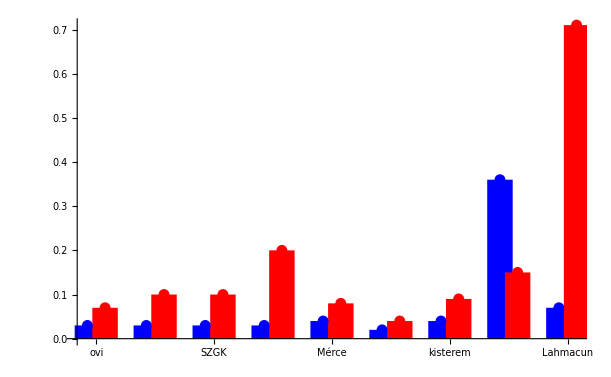

```mathematica
alma=ListPlot[
{
Transpose[{
Range[9]-0.15,
Round[roomCoolingCoefficientEstimates,0.01][[roomsWithTempData]]
}],
Transpose[{
Range[9]+0.15,
Round[roomWarmingCoefficientEstimates,0.01][[roomsWithTempData]]
}]
},
PlotRange->All,PlotStyle->{Blue,Red},Filling->Axis,FillingStyle->{Thickness[0.03]},
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/2]&,roomNames[[roomsWithTempData]]]}],Automatic}
]
```

```mathematica
Export[NotebookDirectory[]<>"\\dbu_1.png",alma]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\dbu_1.png

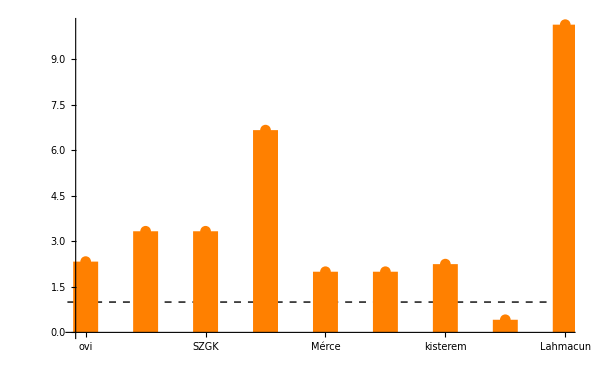

```mathematica
ListPlot[
Round[roomWarmingCoefficientEstimates,0.01][[roomsWithTempData]]/Round[roomCoolingCoefficientEstimates,0.01][[roomsWithTempData]],
PlotRange->All,PlotStyle->{Orange},Filling->Axis,FillingStyle->{Thickness[0.03]},
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/2]&,roomNames[[roomsWithTempData]]]}],Automatic},
Prolog->{Dashed,Line[{{0,1},{10,1}}]}
]
```

### hőfelvételi arányok szobánként

mit:
	- hőtranszfer megbecslése egy körre egy napra csak a hőmérsékleti adatokból
sanity checkek:
	- ennek összevetése a mért hőleadással
	- leadott hő összevetése felvett hővel
	
mi látszik?
	- sok esetben jól korrelál a körön leadott teljes hő és a szobák által hőmérsékleti adatokból leadott hő
	- ami alapján meg lehet becsülni, hogy a szobák hogyan aránylanak egymáshoz
	- vagyis a mért hőleadási adatokból szét lehet osztani a hőfogyasztást szobákra

Sun 31 Dec 2023 00:00:00GMT+2

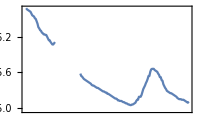
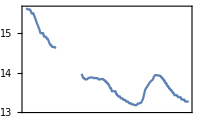
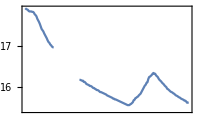
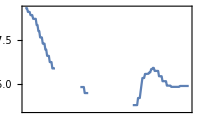

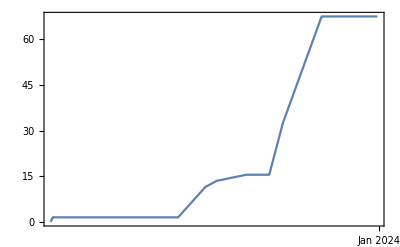
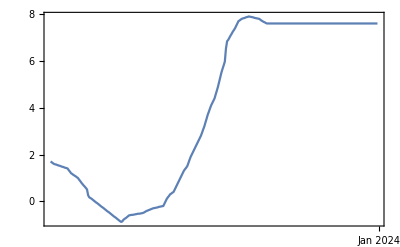

```mathematica
cycle=2;
roomsOnCycle=Flatten[Position[roomToCycle,2]];
day=heatDataDays[[40]]
dayN=Position[seasonDays,day][[1]][[1]];
Row[Table[DateListPlot[roomTempsDaily[[room]][[dayN]][[1]],ImageSize->200],{room,roomsOnCycle}]]
Row[{DateListPlot[heatStockDaily[[cycle]][[dayN]],ImageSize->400],DateListPlot[externalTempDaily[[dayN]],ImageSize->400]}]
```

```mathematica
fullHeatDynamics=Quiet[
Table[
Table[
Table[
Module[
{dayN,roomTemp,externalTemp,tempDiff,roomExternalWallArea,heatLoss,roomRadiatorArea,heatGain},
dayN=Position[seasonDays,day][[1]][[1]];
roomTemp=Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]];
externalTemp=Transpose[externalTempDaily[[dayN]]][[2]];
tempDiff=roomTemp-externalTemp;
roomExternalWallArea=roomExternalWallLength[[room]]roomHeight;
roomRadiatorArea=roomRadiatorLength[[room]]radiatorHeight 2;
heatLoss=roomCoolingCoefficientEstimates[[room]] roomExternalWallArea tempDiff;
heatGain=roomWarmingCoefficientEstimates[[room]] roomRadiatorArea (Map[HeatingCurve[#,65,45]&,Transpose[externalTempDaily[[dayN]]][[2]]]-roomTemp);
Transpose[{
Transpose[externalTempDaily[[dayN]]][[1]],
Transpose[heatingStateDaily[[dayN]][[1+cycle]]][[2]],
100Differences[Transpose[heatStockDaily[[cycle]][[dayN]]][[2]]]//Flatten[{#[[1]],#[[1;;-1]]}]&,
heatGain,
heatLoss,
externalTemp,
roomTemp
}]
]
,{day,Drop[heatDataDays,1]}]
,{room,Flatten[Position[roomToCycle,cycle]]}]
,{cycle,1,3}]
];
```

```mathematica
heatingPeriodHeatDynamics=Table[
roomsOnCycle=Flatten[Position[roomToCycle,cycle]];
Select[
Module[
{dataForSeasonByRoom,heatingStateSwitch,heatingPeriods},
dataForSeasonByRoom=Table[Quiet[Select[Flatten[fullHeatDynamics[[cycle]][[roomOnCycleN]],1],ListQ]],{roomOnCycleN,1,Length[roomsOnCycle]}];
heatingStateSwitch=Differences[Transpose[dataForSeasonByRoom[[1]]][[2]]];
heatingPeriods=Transpose[{
Map[First,Position[heatingStateSwitch,1]],
Map[First,Position[heatingStateSwitch,-1]]
}];
Table[
{
Total[Transpose[dataForSeasonByRoom[[1]][[heatingPeriod[[1]]+1;;Min[heatingPeriod[[2]]+5,Length[dataForSeasonByRoom[[1]]]]]]][[3]]],
Table[
Module[
{heatingPeriodDataForRoom},
heatingPeriodDataForRoom=dataForSeasonByRoom[[roomOnCycleN]][[heatingPeriod[[1]]+1;;Min[heatingPeriod[[2]]+5,Length[dataForSeasonByRoom[[1]]]]]];
If[
Max[Differences[Map[UnixTime,Transpose[heatingPeriodDataForRoom][[1]]]]]<30 60,
Table[Total[Transpose[heatingPeriodDataForRoom][[heatGainOrLoss]]],{heatGainOrLoss,4,5}],
{None,None}
]
],{roomOnCycleN,1,Length[roomsOnCycle]}]
}
,{heatingPeriod,heatingPeriods[[1;;{229,191,208}[[cycle]]]]}]
],ListQ]
,{cycle,1,3}];
```

```mathematica
heatSumsForHeatingPeriods=Quiet[Table[Select[Map[
{
#[[1]],
Total[Transpose[#[[2]]][[1]]],
Total[Transpose[#[[2]]][[2]]]
}
&,heatingPeriodHeatDynamics[[cycle]]
],ListQ],{cycle,1,3}]];
```

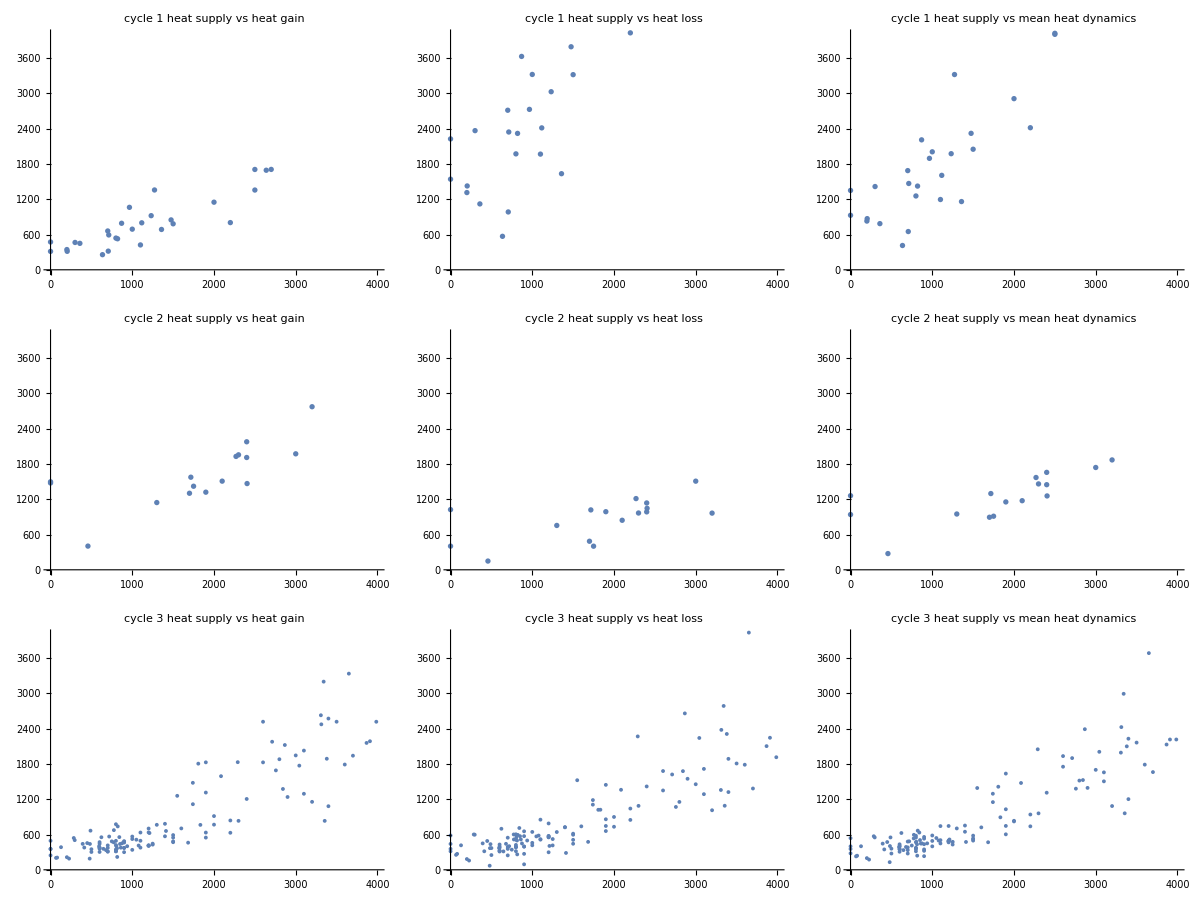

```mathematica
Table[
Join[
Table[
ListPlot[
Quiet[Transpose[Transpose[Select[heatSumsForHeatingPeriods[[cycle]],NumberQ[#[[1]]+#[[heatGainOrLoss]]]&]][[{1,1+heatGainOrLoss}]]]],
ImageSize->300,AspectRatio->1,PlotRange->{{0,4000},{0,4000}},PlotLabel->"cycle "<>ToString[cycle]<>"\nheat supply vs heat "<>{"gain","loss"}[[heatGainOrLoss]]
]
,{heatGainOrLoss,1,2}],
{
ListPlot[
Transpose[{
Quiet[Transpose[Transpose[Select[heatSumsForHeatingPeriods[[cycle]],NumberQ[#[[1]]+#[[heatGainOrLoss]]]&]][[1]]]],
Mean[Transpose[Quiet[Transpose[Transpose[Select[heatSumsForHeatingPeriods[[cycle]],NumberQ[#[[1]]+#[[heatGainOrLoss]]]&]][[{2,3}]]]]]]
}],AspectRatio->1,PlotRange->{{0,4000},{0,4000}},ImageSize->300,PlotLabel->"cycle "<>ToString[cycle]<>"\nheat supply vs mean heat dynamics"
]
}]
,{cycle,1,3}]//Grid
```

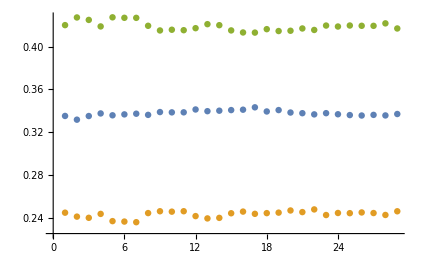
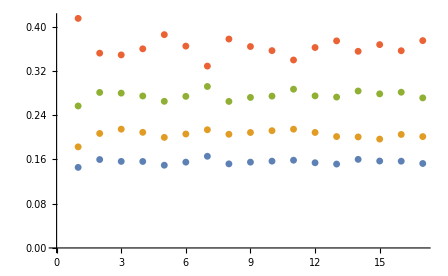
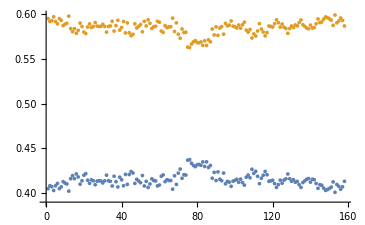

```mathematica
Table[
ListPlot[Transpose[Map[
Transpose[#[[2]]][[heatGainOrLoss]]/Total[Transpose[#[[2]]][[heatGainOrLoss]]]
&,Select[heatingPeriodHeatDynamics[[cycle]],NumberQ[Total[Flatten[#]]]&]
]]],{cycle,1,3}]
```

```mathematica
Map[roomNames[[#]]&,Flatten[Position[roomToCycle,2]]]
```

{SZGK,Gólyairoda,Mérce,Lahmacun}

```mathematica
roomHeatTakeupRatios=Transpose[SortBy[Flatten[Table[
Transpose[{
Flatten[Position[roomToCycle,cycle]],
Mean[
Map[
Transpose[#[[2]]][[heatGainOrLoss]]/Total[Transpose[#[[2]]][[heatGainOrLoss]]]
&,Select[heatingPeriodHeatDynamics[[cycle]],NumberQ[Total[Flatten[#]]]&]
]
]
}],{cycle,1,3}],1],First]][[2]];
```

```mathematica
roomHeatTakeupRatios={0.3377624797730313,0.2430256607463216,0.15551285993802802,0.20516277083684692,0.2755449691581281,0.4148230278815779,0.5851769721184221,None,0.4192118594806471,0.36377940006699705};
```

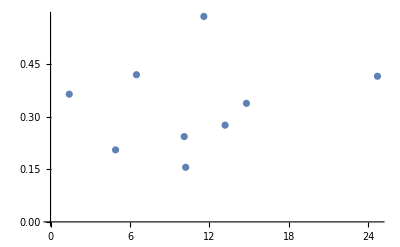

```mathematica
ListPlot[Transpose[{
1/roomWarmingCoefficientEstimates[[roomsWithTempData]],roomHeatTakeupRatios[[roomsWithTempData]]
}]]
```

## szezon teljesítménye

### szobák fogyasztása

```mathematica
roomHeatTakeupDaily=Table[
If[
MemberQ[roomsWithTempData,room],
Table[
If[
Dimensions[heatStockDaily[[1]][[dayN]]]!={},
Transpose[{
Transpose[heatStockDaily[[roomToCycle[[room]]]][[dayN]]][[1]],
Differences[Transpose[heatStockDaily[[roomToCycle[[room]]]][[dayN]]][[2]]]roomHeatTakeupRatios[[room]]//Flatten[{#[[1]],#[[1;;-1]]}]&
}],
None
]
,{dayN,1,Length[seasonDays]}],
None]
,{room,1,10}];
```

```mathematica
o
```

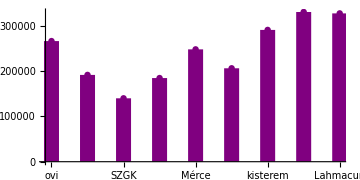

```mathematica
ListPlot[
Table[
Total[gasPricePerCubicMeter Map[
Total[Transpose[#][[2]]]
&,Select[roomHeatTakeupDaily[[room]],Dimensions[#]!={}&]]/(energyContentInGasPerCubicMeter boilerEfficiencyEstimate)]
,{room,roomsWithTempData}],
PlotRange->All,PlotStyle->{Purple},Filling->Axis,FillingStyle->{Thickness[0.03]},AspectRatio->0.5,
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/2]&,roomNames[[roomsWithTempData]]]}],Automatic}
]
```

```mathematica
roomCoolingVsPriceFit=Fit[
Transpose[{
Round[roomCoolingCoefficientEstimates,0.01][[roomsWithTempData]],
Table[
Total[gasPricePerCubicMeter Map[
Total[Transpose[#][[2]]]
&,Select[roomHeatTakeupDaily[[room]],Dimensions[#]!={}&]]/(energyContentInGasPerCubicMeter boilerEfficiencyEstimate)]
,{room,roomsWithTempData}]/1000
}],
{1,Log[x]},
x
];
```

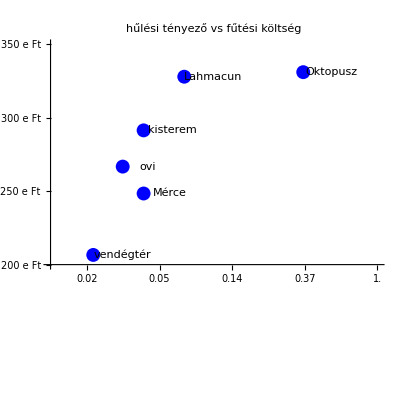

```mathematica
plotData=Transpose[{
Log[Round[roomCoolingCoefficientEstimates,0.01][[roomsWithTempData]]],
Table[
Total[gasPricePerCubicMeter Map[
Total[Transpose[#][[2]]]
&,Select[roomHeatTakeupDaily[[room]],Dimensions[#]!={}&]]/(energyContentInGasPerCubicMeter boilerEfficiencyEstimate)]
,{room,roomsWithTempData}]/1000,
roomNames[[roomsWithTempData]]
}];
ListPlot[
Transpose[Transpose[plotData][[{1,2}]]],
PlotLabel->"hűlési tényező vs fűtési költség",PlotStyle->{PointSize->0.025,Blue},AspectRatio->1,PlotRange->{{-4.5,0},{200,350}},
AxesOrigin->{-4.5,200},Joined->False,
Ticks->{Map[{#,Round[Exp[#],0.01]}&,Range[-4,0,0.5]],Map[{#,ToString[#]<>" e Ft"}&,Range[200,350,50]]},
Epilog->Map[{
Text[#[[3]],#[[{1,2}]]+{0.31+StringLength[#[[3]]]/100,0}]
}&,plotData]
]
```

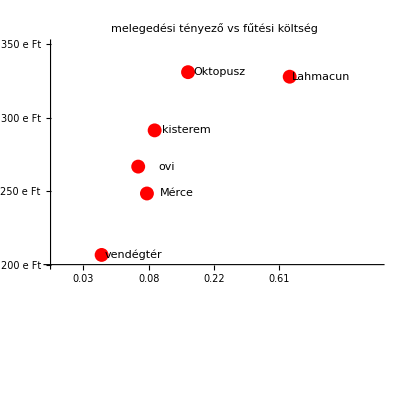

```mathematica
plotData=Transpose[{
Log[Round[roomWarmingCoefficientEstimates,0.01][[roomsWithTempData]]],
Table[
Total[gasPricePerCubicMeter Map[
Total[Transpose[#][[2]]]
&,Select[roomHeatTakeupDaily[[room]],Dimensions[#]!={}&]]/(energyContentInGasPerCubicMeter boilerEfficiencyEstimate)]
,{room,roomsWithTempData}]/1000,
roomNames[[roomsWithTempData]]
}];
ListPlot[
Transpose[Transpose[plotData][[{1,2}]]],
PlotLabel->"melegedési tényező vs fűtési költség",PlotStyle->{PointSize->0.025,Red},AspectRatio->1,PlotRange->{{-4,1},{200,350}},
AxesOrigin->{-4,200},Joined->False,
Ticks->{Map[{#,Round[Exp[#],0.01]}&,Range[-3.5,0,0.5]],Map[{#,ToString[#]<>" e Ft"}&,Range[200,350,50]]},
Epilog->Map[{
Text[#[[3]],#[[{1,2}]]+{0.4+StringLength[#[[3]]]/100,0}]
}&,plotData]
]
```

### szobák céltartása

```mathematica
roomSetTempDiffDaily=Quiet[Table[
If[
MemberQ[roomsWithTempData,room],Table[
If[
Dimensions[roomsWithTempData[[room]][[dayN]]]!={},
Select[
Transpose[
{
Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[1]],
Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]]-Transpose[roomTempsDaily[[room]][[dayN]][[2]]][[2]],
Transpose[heatingStateDaily[[dayN]][[1+roomToCycle[[room]]]]][[2]]
}
],NumberQ[#[[2]]]&],
None
]
,{dayN,1,Length[seasonDays]}],
None]
,{room,1,10}]];
```

### költség vs komfort

```mathematica
roomHeatVsTempDiffDaily=Table[
If[
MemberQ[roomsWithTempData,room],
Select[
Quiet[Transpose[{
Map[
If[
 Dimensions[#]!={},
{
NormalizeDate[Transpose[#][[1]][[1]]],
gasPricePerCubicMeter Total[Transpose[#][[2]]]/(energyContentInGasPerCubicMeter boilerEfficiencyEstimate)
},
None
]&,
roomHeatTakeupDaily[[room]]],
Map[
If[
Dimensions[#]!={}&&#!={},
{
NormalizeDate[Transpose[#][[1]][[1]]],
Mean[Select[Transpose[Transpose[#][[{2,3}]]],#[[2]]==1&]][[1]]
},
None
]&,
roomSetTempDiffDaily[[room]]]
}]],
Dimensions[#[[1]]]!={}&&Dimensions[#[[2]]]!={}&
],
None
],{room,1,10}];
```

```mathematica
extTBinWidth=3;
roomPerformanceExternalTempBins=Table[
If[
MemberQ[roomsWithTempData,room],
Module[
{roomPerformaceCharacteristics,externalTempRange,binnedData},
roomPerformaceCharacteristics=Select[Quiet[Map[
{
Mean[Transpose[externalTempDaily[[Position[Map[NormalizeDate,seasonDays],#[[1]][[1]]][[1]][[1]]]]][[2]]],
#[[1]][[2]],
#[[2]][[2]]
}
&,roomHeatVsTempDiffDaily[[room]]]],NumberQ[Total[#]]&];
externalTempRange=MinMax[Transpose[roomPerformaceCharacteristics][[3]]];
binnedData=Select[Quiet[Table[
{
extT+extTBinWidth,
Transpose[Transpose[Select[roomPerformaceCharacteristics,Between[#[[1]],{extT,extT+extTBinWidth}]&]][[{2,3}]]]
}
,{extT,Floor[externalTempRange[[1]],1],Ceiling[externalTempRange[[2]],1],extTBinWidth}]],NumberQ[Total[Flatten[#]]]&]
],
None
],{room,1,10}];
```

```mathematica
Quiet[Table[
ListPlot[
{},
PlotLabel->roomNames[[room]],
AxesLabel->{Rotate["költség (Ft)",Pi/2],"eltérés (°C)"},
ImageSize->350,
PlotRange->{
{0,
Ceiling[Max[
Map[
#[[1]][[2]]&,
roomHeatVsTempDiffDaily[[room]]]
],500]
},
{-5,6}
},AspectRatio->1,
Prolog->{
Table[
{
RGBColor[
(binData[[1]]+3)/(21-3),
0,
1-(binData[[1]]+3)/(21-3),
0.25
],
EdgeForm[
{
Thick,Dashed,
RGBColor[
(binData[[1]]+3)/(21-3),
0,
1-(binData[[1]]+3)/(21-3),
0.5
]
}
],
Ellipsoid[
GetMeanAndSD[binData[[2]]][[1]],
GetMeanAndSD[binData[[2]]][[2]]0.75
]
},{binData,roomPerformanceExternalTempBins[[room]]}
],
Map[
{
RGBColor[
(#[[1]]+3)/(21-3),
0,
1-(#[[1]]+3)/(21-3),
0.75
],
PointSize->0.0125,
Point[#[[{2,3}]]]
}&,
Select[Quiet[Map[
{
Mean[Transpose[externalTempDaily[[Position[Map[NormalizeDate,seasonDays],#[[1]][[1]]][[1]][[1]]]]][[2]]],
#[[1]][[2]],
#[[2]][[2]]
}
&,roomHeatVsTempDiffDaily[[room]]]],NumberQ[Total[#]]&]
]
}
],{room,roomsWithTempData}]]//ArrayReshape[#,{3,3}]&//Grid
```

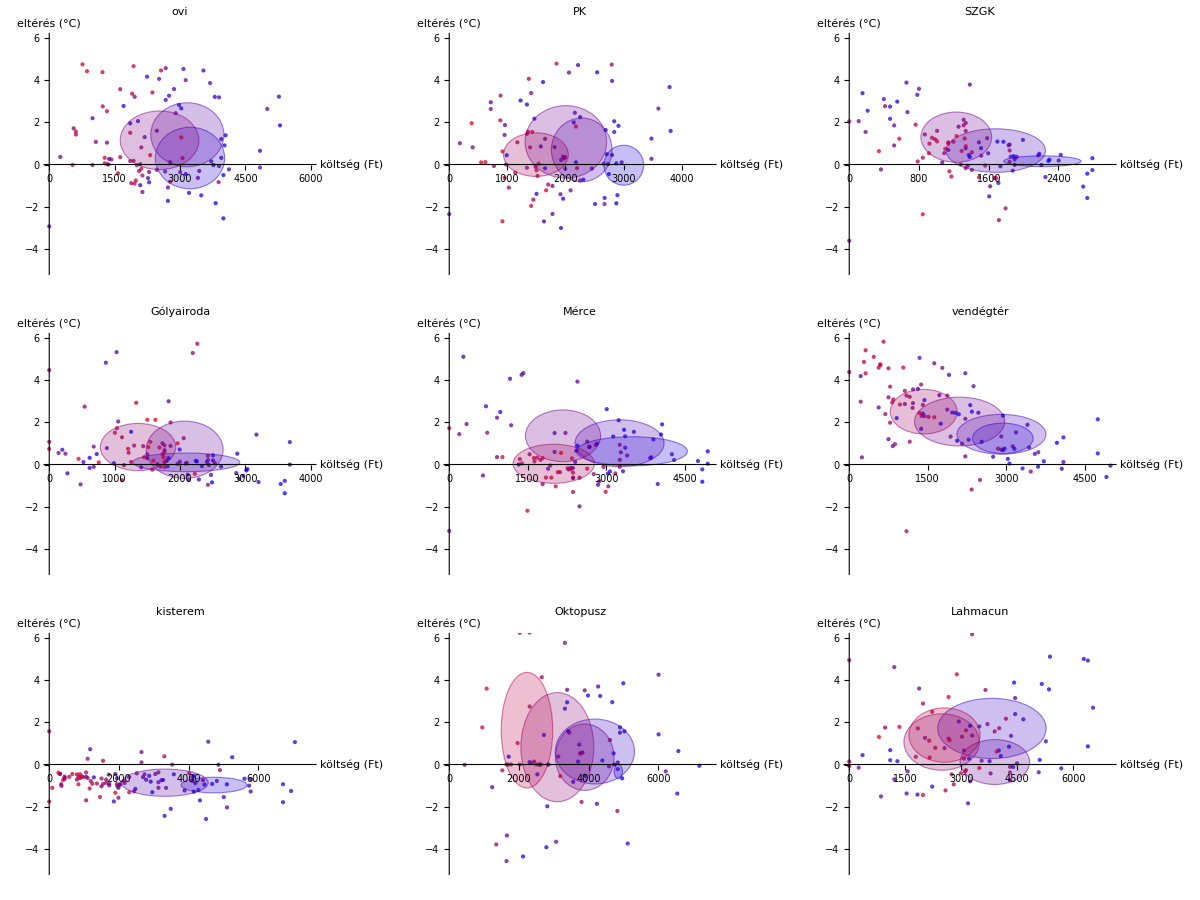
```mathematica
alma=-Graphics-
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"\\dbu_2.png",alma]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\dbu_2.png

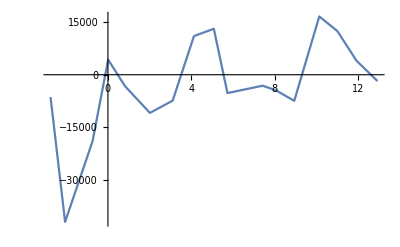
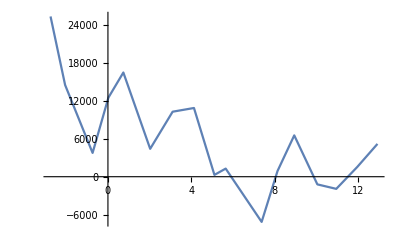
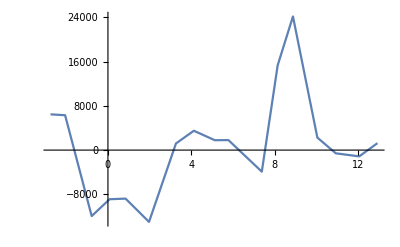
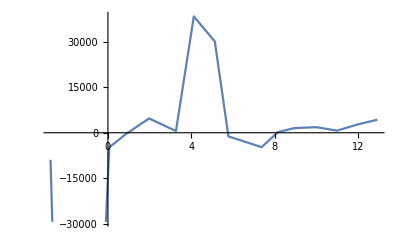
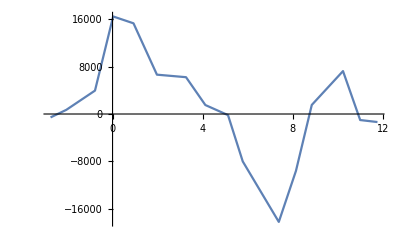
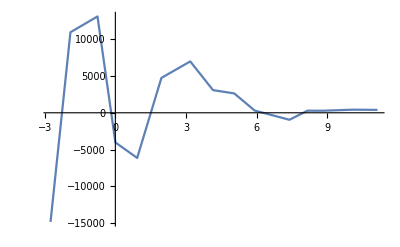
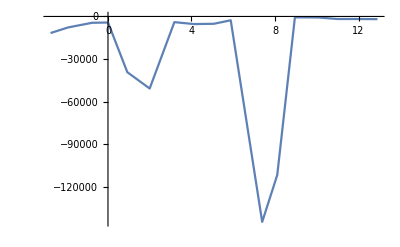
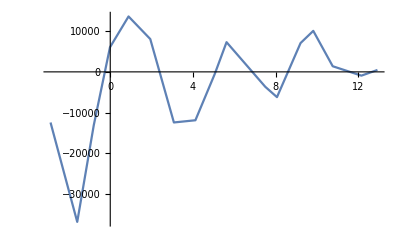

```mathematica
binWidth=2;
binStep=1;
Table[
ListPlot[
Module[
{dataToBin,binRange},
dataToBin=Select[Quiet[Map[
{
Mean[Transpose[externalTempDaily[[Position[Map[NormalizeDate,seasonDays],#[[1]][[1]]][[1]][[1]]]]][[2]]],
#[[1]][[2]]/#[[2]][[2]]
}
&,roomHeatVsTempDiffDaily[[room]]]],NumberQ[Total[#]]&];
binRange=MinMax[Transpose[dataToBin][[1]]];
Table[
Mean[Select[dataToBin,Between[#[[1]],{bin-binWidth/2,bin+binWidth/2}]&]]
,{bin,binRange[[1]],binRange[[2]],binStep}]
],Joined->True
],{room,roomsWithTempData}]
```

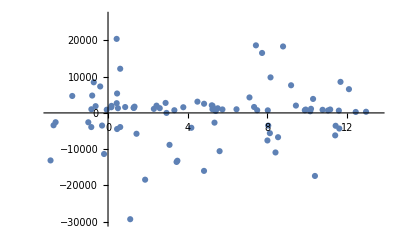
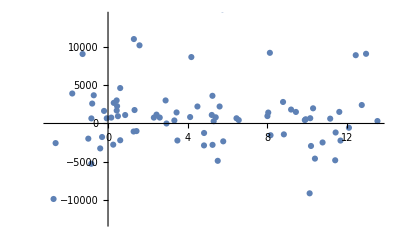
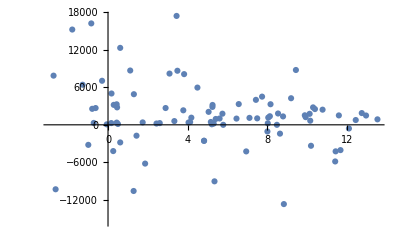
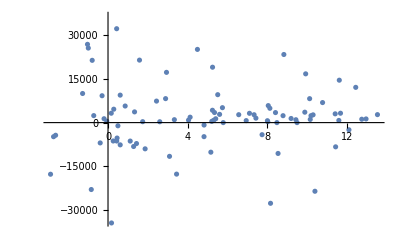
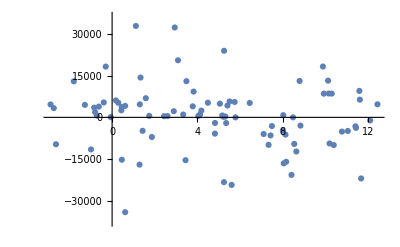
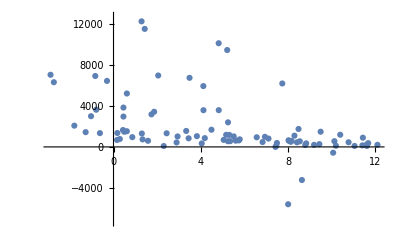
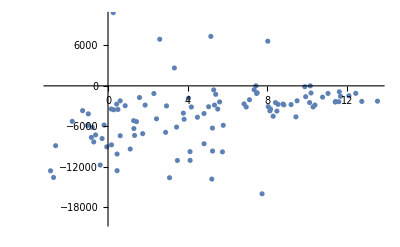
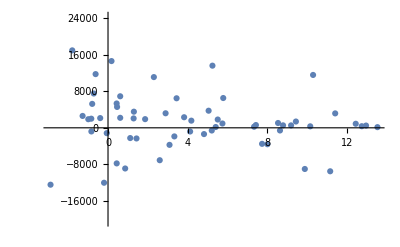

```mathematica
Table[
ListPlot[
Select[Quiet[Map[
{
Mean[Transpose[externalTempDaily[[Position[Map[NormalizeDate,seasonDays],#[[1]][[1]]][[1]][[1]]]]][[2]]],
#[[1]][[2]]/#[[2]][[2]]
}
&,roomHeatVsTempDiffDaily[[room]]]],NumberQ[Total[#]]&]
],{room,roomsWithTempData}]
```

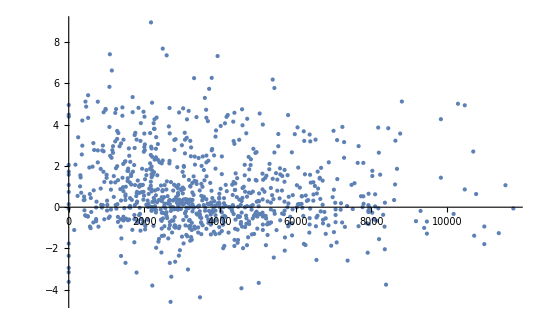

```mathematica
ListPlot[
Flatten[Table[
Select[Map[
{
#[[1]][[2]],
Quiet[#[[2]][[2]]]
}
&,roomHeatVsTempDiffDaily[[room]]],NumberQ[Total[#]]&]
,{room,roomsWithTempData}],1]
]
```

## szimuláció

- megnézni azt is, hogy a nem outlierek közti különbségek miből eredhetnek

## egy szoba, egy nap

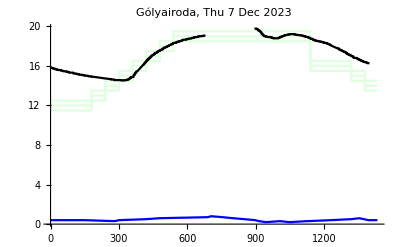

```mathematica
dayN=30;
room=4;

massOfAirInRoom=roomAreas[[room]]roomHeight airSpecificMass;
externalWallArea=roomExternalWallLength[[room]] roomHeight;
radiatorArea=roomRadiatorLength[[room]]radiatorHeight 2;
roomHeatCapacity=massOfAirInRoom airSpecificHeatCapacity;
startTimeBin=4;
heatingStateStart=Transpose[heatingStateDaily[[dayN]][[1+roomToCycle[[room]]]]][[2]][[startTimeBin]];
roomSetTemp=Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayN]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,roomTempsDaily[[room]][[dayN]][[2]]
],
InterpolationOrder->0
];
roomTempStart=Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]][[startTimeBin]];
roomLowerBuffer=Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayN]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,roomTempsDaily[[room]][[dayN]][[3]]
],
InterpolationOrder->0
];
roomUpperBuffer=Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayN]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,roomTempsDaily[[room]][[dayN]][[4]]
],
InterpolationOrder->0
];
externalTemp=Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayN]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,externalTempDaily[[dayN]]
],
InterpolationOrder->1
];
roomTrueTemp=Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayN]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,roomTempsDaily[[room]][[dayN]][[1]]
],
InterpolationOrder->0
];
Plot[
{
roomSetTemp[t],
roomSetTemp[t]-roomLowerBuffer[t],
roomSetTemp[t]+roomUpperBuffer[t],
externalTemp[t],
roomTrueTemp[t]
},{t,0,24 60-5},PlotStyle->{LightGreen,LightGreen,LightGreen,Blue,Black},
PlotRange->All,PlotLabel->roomNames[[room]]<>", "<>DateString[NormalizeDate[seasonDays[[dayN]]]]
]
```

```mathematica
warmingCorrection=1.5;
```

```mathematica
timeScaling= 1/(60);
dt=5;
tStart=dt startTimeBin;
tEnd=24 60-5;
simulation=Module[
{roomTemp,roomTempList,heatingState,heatingStateList,τStart,τEnd,dτ},
roomTemp=roomTempStart;
heatingState=heatingStateStart;
τStart=tStart/timeScaling;
τEnd=tEnd/timeScaling;
dτ=dt/timeScaling;

roomTempList={};
heatingStateList={};
Table[
Module[
{warming,cooling,dRoomTemp},
roomTempList=If[
roomTempList=={},
{{timeScaling τ,roomTemp}},
Join[roomTempList,{{timeScaling τ,roomTemp}}]
];
heatingStateList=If[
heatingStateList=={},
{{timeScaling τ,heatingState}},
Join[heatingStateList,{{timeScaling τ,heatingState}}]
];

warming=warmingCorrection heatingState roomWarmingCoefficientEstimates[[room]] radiatorArea(HeatingCurve[externalTemp[timeScaling τ],75,45]-roomTemp);
cooling=(roomCoolingCoefficientEstimates[[room]])externalWallArea(roomTemp-externalTemp[timeScaling τ]);

dRoomTemp=dτ (warming-cooling)/roomHeatCapacity;

roomTemp+=dRoomTemp;
heatingState=If[
roomTemp<roomSetTemp[timeScaling τ]-roomLowerBuffer[timeScaling τ]&&roomTemp-roomTempList[[-1]][[2]]<0,
1,
If[
roomTemp>roomSetTemp[timeScaling τ]+roomUpperBuffer[timeScaling τ]&&roomTemp-roomTempList[[-1]][[2]]>0,
0,
heatingState
]
];
]
,{τ,τStart,τEnd,dτ}];
{
Drop[heatingStateList,1],
Drop[roomTempList,1]
}
];
```

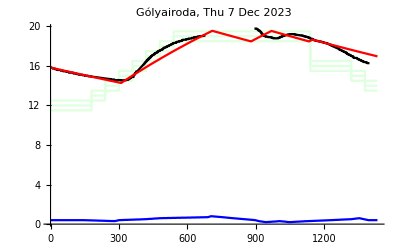

```mathematica
roomSimulatedTemp=Interpolation[simulation[[2]],InterpolationOrder->1];
Quiet[Plot[
{
roomSetTemp[t],
roomSetTemp[t]-roomLowerBuffer[t],
roomSetTemp[t]+roomUpperBuffer[t],
externalTemp[t],
roomTrueTemp[t],
roomSimulatedTemp[t]
},{t,0,24 60-5},PlotStyle->{LightGreen,LightGreen,LightGreen,Blue,Black,Red},
PlotRange->All,PlotLabel->roomNames[[room]]<>", "<>DateString[NormalizeDate[seasonDays[[dayN]]]]
]]
```

## egy kör, egy nap

```mathematica
dayN=78;
cycle=2;
roomsOnCycle=Flatten[Position[roomToCycle,cycle]]
massOfAirInRoom=Table[roomAreas[[room]]roomHeight airSpecificMass,{room,roomsOnCycle}];
externalWallArea=Table[roomExternalWallLength[[room]] roomHeight,{room,roomsOnCycle}];
radiatorArea=Table[roomRadiatorLength[[room]]radiatorHeight 2,{room,roomsOnCycle}];
roomHeatCapacity=Table[roomAreas[[room]]roomHeight airSpecificMass airSpecificHeatCapacity,{room,roomsOnCycle}];
```

{3,4,5,10}

InterpolatingFunction::dmval: Input value {0.029315} lies outside the range of data in the interpolating function. Extrapolation will be used.

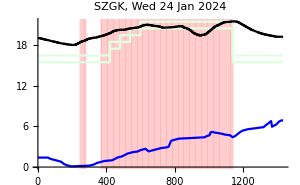
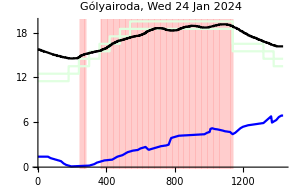
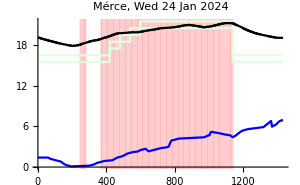
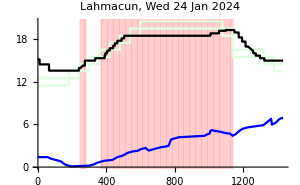

```mathematica
startTimeBin=1;
heatingStateStart=Transpose[heatingStateDaily[[dayN]][[1+cycle]]][[2]][[startTimeBin]];
heatingTrueState=Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayN]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[heatingStateDaily[[dayN]][[1+cycle]],#[[2]]!="n"&]
],
InterpolationOrder->0
];
roomSetTemp=Table[
Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayN]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[roomTempsDaily[[room]][[dayN]][[2]],#[[2]]!="n"&]
],
InterpolationOrder->0
],{room,roomsOnCycle}];
roomLowerBuffer=Table[
Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayN]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[roomTempsDaily[[room]][[dayN]][[3]],#[[2]]!="n"&]
],
InterpolationOrder->0
]
,{room,roomsOnCycle}];
roomUpperBuffer=Table[
Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayN]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[roomTempsDaily[[room]][[dayN]][[4]],#[[2]]!="n"&]
],
InterpolationOrder->0
]
,{room,roomsOnCycle}];
roomTrueTemp=Table[
Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayN]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[roomTempsDaily[[room]][[dayN]][[1]],#[[2]]!="n"&]
],
InterpolationOrder->0
]
,{room,roomsOnCycle}];
externalTemp=Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayN]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[externalTempDaily[[dayN]],#[[2]]!="n"&]
],
InterpolationOrder->1
];
Table[
Plot[
{
roomSetTemp[[roomN]][t]-roomLowerBuffer[[roomN]][t],
roomSetTemp[[roomN]][t],
roomSetTemp[[roomN]][t]+roomUpperBuffer[[roomN]][t],
externalTemp[t],
roomTrueTemp[[roomN]][t]
},{t,0,24 60-5},PlotStyle->{LightGreen,None,LightGreen,Blue,Black},
PlotRange->All,PlotLabel->roomNames[[roomsOnCycle[[roomN]]]]<>", "<>DateString[NormalizeDate[seasonDays[[dayN]]]],ImageSize->300,
Prolog->Table[If[
heatingTrueState[t]==1,
{RGBColor[1,0,0,0.1],Rectangle[{t,-100},{t+5,100}]},
Nothing
]
,{t,0,24 60 -5,5}]
],{roomN,1,Length[roomsOnCycle]}]//Row
```

```mathematica
roomsOnCycle
```

{1,2,9}

```mathematica
roomNames[[1;;10]]
```

{ovi,PK,SZGK,Gólyairoda,Mérce,vendégtér,kisterem,trafóház,Oktopusz,Lahmacun}

```mathematica
warmingCorrection={1.5,1.5,1.25,1.25,1.5,1,1,1,1,0.9};
```

```mathematica
coolingCorrection={1,1,1,1,1,1,1,1,1,1.3};
```

```mathematica
Position[warmingCorrection,1.5]
```

{{1},{2},{3},{4},{5},{9}}

```mathematica
timeScaling= 1/(60);
dt=5;
tStart=dt startTimeBin;
tEnd=24 60;
roomTempStart=Table[roomTrueTemp[[roomN]][tStart],{roomN,1,Length[roomsOnCycle]}];
simulation=Module[
{roomTemp,roomTempList,heatingState,heatingStateList,τStart,τEnd,dτ},
roomTemp=roomTempStart;
heatingState=heatingStateStart;
τStart=tStart/timeScaling;
τEnd=tEnd/timeScaling;
dτ=dt/timeScaling;

roomTempList=Table[{},{roomN,1,Length[roomsOnCycle]}];
heatingStateList={};
Table[
Module[
{heatingStateVotes},
heatingStateVotes=
Table[
Module[
{warming,cooling,dRoomTemp,heatingStateVote},

roomTempList[[roomN]]=If[
roomTempList[[roomN]]=={},
{{timeScaling τ,roomTemp[[roomN]]}},
Join[roomTempList[[roomN]],{{timeScaling τ,roomTemp[[roomN]]}}]
];

warming=warmingCorrection[[roomsOnCycle[[roomN]]]] heatingState roomWarmingCoefficientEstimates[[roomsOnCycle[[roomN]]]] radiatorArea[[roomN]](HeatingCurve[externalTemp[timeScaling τ],75,45]-roomTemp[[roomN]]);
cooling=coolingCorrection[[roomsOnCycle[[roomN]]]](roomCoolingCoefficientEstimates[[roomsOnCycle[[roomN]]]])externalWallArea[[roomN]](roomTemp[[roomN]]-externalTemp[timeScaling τ]);

dRoomTemp=dτ (warming-cooling)/roomHeatCapacity[[roomN]];

roomTemp[[roomN]]+=dRoomTemp;
heatingStateVote=If[
roomTemp[[roomN]]<roomSetTemp[[roomN]][timeScaling τ]-roomLowerBuffer[[roomN]][timeScaling τ]&&dRoomTemp<0,
1,
If[
roomTemp[[roomN]]>roomSetTemp[[roomN]][timeScaling τ]+roomUpperBuffer[[roomN]][timeScaling τ]&&dRoomTemp>0,
0,
heatingState
]
];
heatingStateVote
]
,{roomN,1,Length[roomsOnCycle]}];

heatingStateList=If[
heatingStateList=={},
{{timeScaling τ,heatingState}},
Join[heatingStateList,{{timeScaling τ,heatingState}}]
];

heatingState=Max[heatingStateVotes]

]
,{τ,τStart,τEnd,dτ}];
{
heatingStateList,
roomTempList
}
];
simulatedHeatDynamics=Table[Module[
{roomTemp,externalTemp,tempDiff,roomExternalWallArea,heatLoss,roomRadiatorArea,heatGain},
roomTemp=Transpose[simulation[[2]][[roomN]]][[2]];
externalTemp=Transpose[externalTempDaily[[dayN]]][[2]];
tempDiff=roomTemp-externalTemp;
roomExternalWallArea=roomExternalWallLength[[roomsOnCycle[[roomN]]]]roomHeight;
roomRadiatorArea=roomRadiatorLength[[roomsOnCycle[[roomN]]]]radiatorHeight 2;
heatLoss=coolingCorrection[[roomsOnCycle[[roomN]]]]roomCoolingCoefficientEstimates[[roomsOnCycle[[roomN]]]] roomExternalWallArea tempDiff;
heatGain=warmingCorrection[[roomsOnCycle[[roomN]]]]roomWarmingCoefficientEstimates[[roomsOnCycle[[roomN]]]] roomRadiatorArea (Map[HeatingCurve[#,75,45]&,Transpose[externalTempDaily[[dayN]]][[2]]]-roomTemp);
{
heatLoss,
heatGain
}
],{roomN,1,Length[roomsOnCycle]}];
```

InterpolatingFunction::dmval: Input value {5} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1440} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

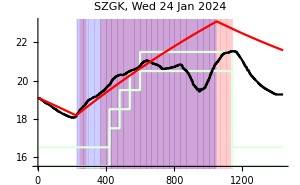
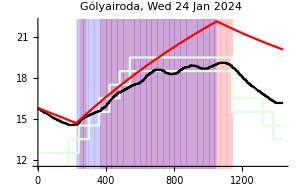
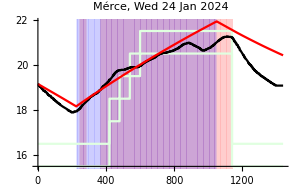
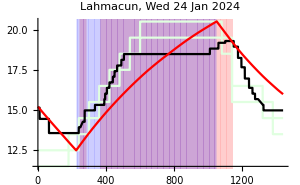

{18500.,16294.2,34747.8,25521.}

```mathematica
heatingSimulatedState=Interpolation[simulation[[1]],InterpolationOrder->1];
roomSimulatedTemp=Table[Interpolation[simulation[[2]][[roomN]],InterpolationOrder->1],{roomN,1,Length[roomsOnCycle]}];
Table[
Quiet[Plot[
{
roomSetTemp[[roomN]][t]-roomLowerBuffer[[roomN]][t],
roomSetTemp[[roomN]][t],
roomSetTemp[[roomN]][t]+roomUpperBuffer[[roomN]][t],
roomTrueTemp[[roomN]][t],
roomSimulatedTemp[[roomN]][t]
},{t,0,24 60},PlotStyle->{LightGreen,None,LightGreen,Black,Red},
PlotRange->All,PlotLabel->roomNames[[roomsOnCycle[[roomN]]]]<>", "<>DateString[NormalizeDate[seasonDays[[dayN]]]],ImageSize->300,
Prolog->{
Table[If[
heatingTrueState[t]==1,
{RGBColor[1,0,0,0.1],Rectangle[{t,-100},{t+5,100}]},
Nothing
]
,{t,0,24 60 -5,5}],
Table[If[
heatingSimulatedState[t]==1,
{RGBColor[0,0,1,0.1],Rectangle[{t,-100},{t+5,100}]},
Nothing
]
,{t,0,24 60 -5,5}]
}
]
],{roomN,1,Length[roomsOnCycle]}]//Row
Join[
{100heatStockDaily[[cycle]][[dayN]][[-1]][[2]]},
Total[Map[
Map[Total,#]
&,simulatedHeatDynamics]],
{
Mean[Total[Map[
Map[Total,#]
&,simulatedHeatDynamics]]]
}
]
```